-Graphics-

Make: Matrices & Geometry
Authors:  Bill Davis and Jerry Uhl  ©1996-2010
Publisher:  Make: Mathematics

# MGM.04 SVD Analysis of 2D Matrices LITERACY

Mathematica 8.0 Initializations

```mathematica
Off[General::"spell"];
  Off[General::"spell1"];  
Off[SingularValues::"deprec"];  

Needs["Units`"];  

SetOptions[ListAnimate, AnimationRepetitions -> 4];  
SetOptions[Animate, AnimationRepetitions -> 4];  
CMView={2.7,1.6,1.2};
```

#### Vector Drawer

```mathematica
(* :Date:  Copyright 1993-2011, Math Everywhere, Inc. 
*)
(*
Original Conception to create a vector drawer is due to Bill Davis.
Current code is by Bruce Carpenter.
*)
(*  :Drawbacks:  Since the vectors are drawn out of 
     context, the shapes of the arrowheads are only 
     correct with AspectRatio set to Automatic.
*)
```

```mathematica
BeginPackage["Vector3D`"];
```

```mathematica
Axes3D::usage="Axes3D[a, b] creates a Graphics3D object of cartesian axes with x, y, and z running from -a/3 to a, and with axes labels b units beyond the tips of the axes.  Axes3D[a] is Axes3D[a, a/8].";
Perpend::usage="Perpend[a] returns a unit vector which is perpendicular to the vector a.";
Vector::usage="Vector[a] produces a 2 or 3 dimensional vector from the origin to a. Arrow[a, Tail → tail] gives a vector from tail to a.";
CandMArrow::usage="CandMArrow[a, b] gives a 2D or 3D arrow from a to b.";
VectorHead::usage="VectorHead[a, vec] produces an arrowhead with its tip placed at the point a, pointing in the direction of the vector vec.";
Tail::usage="Tail → point puts the tail of the vector at point.";
Aperture::usage="Aperture is the ratio of the radius of the base to the length of the head of a vector.";
TipSize::usage="TipSize specifies an absolute size for the inner tip length of the head of a vector.";
TipRatio::usage="TipRatio is the ratio of the inner length of the arrowhead to the length of the shaft of a vector.";
HeadRatio::usage="HeadRatio is the ratio of the outer length of the arrowhead to the length of the shaft of a vector.";
HeadSize::usage="HeadSize specifies an absolute size for the head of a vector.";
ScaleFactor::usage="ScaleFactor specifies the amount to scale a vector in length and may be either a number or a pure function.";
ZeroVectorPointSize::usage="ZeroVectorPointSize is the size of the point used to represent a zero vector.";
Options[Vector]=Options[CandMArrow]=Options[VectorHead]={HeadRatio->0.18,TipRatio->0.14,Aperture->0.3,ScaleFactor->1,HeadType->Polygon,ShaftQ->True,EdgesQ->True,VectorColor->RGBColor[0,0,1],ShaftWidth->0.005,ZeroVectorPointSize->0.01};
Begin["`Private`"];
SetOptions[ParametricPlot,AspectRatio->Automatic];
SetOptions[Plot,AspectRatio->Automatic];
SetOptions[Graphics,AspectRatio->Automatic];
Axes3D[u_,v_]:=Graphics3D[{{Blue,Line[{{-u/3,0,0},{u,0,0}}]},Text["x",{u+v,0,0}],{Blue,Line[{{0,-u/3,0},{0,u,0}}]},Text["y",{0,u+v,0}],{Blue,Line[{{0,0,-u/3},{0,0,u}}]},Text["z",{0,0,u+v}]}];
Axes3D[u_]:=Axes3D[u,u/8];
Perpend[a_?VectorQ]:=Normalize[{a⟦2⟧,-a⟦1⟧}]/;Length[a]==2;
Perpend[a_?VectorQ]:=Normalize[If[a⟦1⟧==0,{1,0,0},{a⟦2⟧,-a⟦1⟧,0}]]/;Length[a]==3;
Base3D=Table[{Cos[(2 k π)/8.],Sin[(2 k π)/8.]},{k,0,8}];
CandMArrow[from_?VectorQ,to_?VectorQ,opts___]:=Module[{sq,sw,ht,hs,hr,tr,ap,sf,vc,zvps,diff=to-from,tip},{sq,sw,ht,hs,hr,ts,tr,ap,sf,vc,zvps}={ShaftQ,ShaftWidth,HeadType,HeadSize,HeadRatio,TipSize,TipRatio,Aperture,ScaleFactor,VectorColor,ZeroVectorPointSize}/.{opts}/.Options[Vector];If[from==to,Return[Graphics[{PointSize[zvps],vc,Point[from]}]]];diff=If[NumberQ[N[sf]],sf diff,sf[diff]];tip=from+diff;If[NumberQ[hs],hr=hs/Norm[diff];tr=0.75 hr];If[NumberQ[ts],tr=ts/Norm[diff]];Graphics[{If[sq,{vc,Thickness[sw],Line[{from,tip-tr diff}]},{}],With[{trans=ap hr Norm[diff] Perpend[diff]},{vc,Thickness[sw],ht[{tip,tip-hr diff+trans,tip-tr diff,tip-hr diff-trans,tip}]}]}]]/;Length[from]==Length[to]==2
CandMArrow[from_?VectorQ,to_?VectorQ,opts___]:=Module[{sq,eq,sw,hs,hr,tr,ap,sf,vc,zvps,diff=to-from,tip},{sq,eq,sw,hs,hr,ap,sf,vc,zvps}={ShaftQ,EdgesQ,ShaftWidth,HeadSize,HeadRatio,Aperture,ScaleFactor,VectorColor,ZeroVectorPointSize}/.{opts}/.Options[Vector];If[from==to,Return[Graphics3D[{PointSize[zvps],vc,Point[from]}]]];diff=If[NumberQ[N[sf]],sf diff,sf[diff]];tip=from+diff;If[NumberQ[hs],hr=hs/Norm[diff]];tr=hr/2;Graphics3D[{If[sq,{vc,Thickness[sw],Line[{from,tip-tr diff}]},{}],If[eq,{},EdgeForm[]],{SurfaceColor[vc],With[{temp=Perpend[diff]},(Polygon[Append[#1,tip]]&)/@Partition[(tip-hr diff+#1&)/@((ap hr Norm[diff] Base3D).{temp,Normalize[temp×diff]}),2,1]]}}]]/;Length[from]==Length[to]==3
Vector[a_,Tail->b_,opts___]:=CandMArrow[b,a+b,opts]
Vector[a_,opts___]:=CandMArrow[Table[0,{Length[a]}],a,opts]
VectorHead[a_,b_,opts___]:=CandMArrow[a-b,a,ShaftQ->False,opts];
End[];
EndPackage[];
```

```mathematica
Graphics`Colors`GosiaGreen=RGBColor[0, 0.392187, 0];
```

#### ThreeAxes[u,v]

```mathematica
ThreeAxes[u_,v_]:=Graphics3D[{{Blue,Line[{{-u,0,0},{u,0,0}}]},Text["x",{u+v,0,0}],{Blue,Line[{{0,-u,0},{0,u,0}}]},Text["y",{0,u+v,0}],{Blue,Line[{{0,0,0},{0,0,u}}]},Text["z",{0,0,u+v}]}];
ThreeAxes[u_]:=ThreeAxes[u,u/8];
ThreeAxes::"usage"="ThreeAxes[a,b] makes a standard cartesian axis graphics object with x, y, and z running from -a to a, and with axis labels b units beyond the tips of the axes.  ThreeAxes[a] is ThreeAxes[a,a/8].";
```

What you should be able to handle when you are away from the machine.

#### L.1)

Explain this:
Given a 2D matrix A, if you can come up with an s (in radians) so that
   A.{Cos[s],Sin[s]} is perpendicular to A.{Cos[s+π/2],Sin[s+π/2]}, then you can read off 
   1) SVD aligner for A
   2) SVD stretchfactors for A
   3) SVD hanger for A

#### L.2)

Here's a random 2D matrix A:

```mathematica
A = {{Random[Real,{2,3}],Random[Real,{0.5,1.5}]},
             {Random[Real,{1,1.5}],Random[Real,{-2,-1}]}};
MatrixForm[A]
```

(2.6879 | 1.3468
1.45803 | -1.32374)

Here's the ellipse you get when you hit this matrix on the unit circle centered at {0,0}:

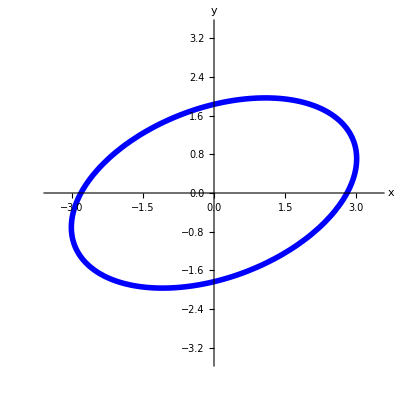

```mathematica
ranger =1.1 Max[SingularValues[A][[2]]]; 
Clear[t];
ellipseplot = ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->{{Thickness[0.01],Blue}},AxesLabel->{"x","y"},PlotRange->{{-ranger,ranger},{-ranger,ranger}}]
```

The SVD hanger matrix for A is:

```mathematica
hanger=Transpose[SingularValues[A]⟦1⟧];
MatrixForm[hanger]
```

(-0.940817 | 0.338915
-0.338915 | -0.940817)

The SVD stretcher matrix for A is:

```mathematica
stretcher=DiagonalMatrix[SingularValues[A]⟦2⟧];
MatrixForm[stretcher]
```

(3.1318 | 0.
0. | 1.76312)

The SVD aligner matrix for A is:

```mathematica
aligner=SingularValues[A]⟦3⟧;
MatrixForm[aligner]
```

(-0.965247 | -0.261338
-0.261338 | 0.965247)

Fill the blanks:
The length of the long axis of this ellipse is ....................
The length of the short axis of this ellipse is....................
The perpendicular frame {perpframe[1],perpframe[2]} that defines the long and the short axes of this ellipse is 
              perpframe[1] = {.........................., ......................}
              perpframe[2] = {.........................., ......................}
The area enclosed by this ellipse is (...............................) times (............................)  times π.

#### L.3)

Given a 2D matrix A how do you use the SVD stretch factors of A to determine whether A is invertible?

#### L.4)

Given a 2D matrix A how do you use the SVD stretch factors of A to determine the rank of A?

#### L.5)

Lots of folks like to say that a given 2D matrix A is:
→ invertible if Det[A] ≠ 0
→ not invertible if Det[A] = 0.
Explain why they are right.

#### L.6)

Given a 2D matrix A you do an SVD analysis and get
            A = hanger.(a | 0
0 | b).aligner.
with a and b both positive. 
This information tells you that given any 2D vector Y, there is exactly one 2D vector X with A.X = Y.
Agree........................................
Disagree........................................

#### L.7)

Given a 2D matrix A you do an SVD analysis and get
            A = hanger.(a | 0
0 | 0).aligner.
with a > 0. 
This information tells you that the rank of A is ......................

#### L.8)

Given a 2D matrix A you do an SVD analysis and get
            A = hanger.(a | 0
0 | 0).aligner.
with a >0. 
This information tells you that if a 2D vector Y is on a certain line through {0,0}, then there is exactly one 2D vector X with A.X = Y.
Agree........................................
Disagree........................................

#### L.9)

Given a 2D matrix A you do an SVD analysis and get
            A = hanger.(1.234 | 0
0 | 0.0).aligner.
This information tells you that given a 2D vector Y, then  either
A.X = Y has no solution X or A.X = Y has many solutions X.
.
Agree........................................
Disagree........................................

#### L.10)

Given a 2D matrix A you do an SVD analysis and get
            A = hanger.(3.0 | 0
0 | 2.0).aligner.
You plot the SVD aligner frame and learn it is a right hand perpendicular frame.
You plot the SVD hanger frame and learn it is a right hand perpendicular frame.
Fill the blank:
Det[A] = .........................................

#### L.11)

Given a 2D matrix A you do an SVD analysis and get
            A = hanger.(2.0 | 0
0 | 5.0).aligner.
You plot the SVD aligner frame and learn it is a left hand perpendicular frame.
You plot the SVD hanger frame and learn it is a left hand perpendicular frame.
Fill the blank:
Det[A] = .........................................

#### L.12)

You are given a 2D matrix A and learn that  Det[A] < 0. This tells you that a hit with A incorporates a flip.
Agree....... Disagree........

#### L.13)

You are given a 2D matrix A and learn that  Det[A] > 0. This tells you that  a hit with A incorporates no flip.
Agree....... Disagree........

#### L.14)

Given a 2D matrix A you do an SVD analysis and get
            A = hanger.(4.0 | 0
0 | 0.5).aligner.
You plot the SVD aligner frame and learn it is a right hand perpendicular frame.
You plot the SVD hanger frame and learn it is a left hand perpendicular frame.
Fill the blank:
Det[A] = .........................................

#### L.15)

Given a 2D matrix A you do an SVD analysis and get
            A = hanger.(3.0 | 0
0 | 2.0).aligner.
You plot the aligner frame and learn it is a left hand perpendicular frame.
You plot the hanger frame and learn it is a right hand perpendicular frame.
Fill the blank:
Det[A] = .........................................

#### L.16)

Given a 2D matrix A you do an SVD analysis and get
             A =  hanger.(a | 0
0 | b). aligner.
Using this, you can compute A^tvia the formula:

a)  A^t =  aligner.(b | 0
0 | a). hanger             b)  A^t =  hanger^t.(b | 0
0 | a). aligner^t

c)  A^t =  aligner^t.(a | 0
0 | b). hanger^t         d)  A^t =  aligner^t.(b | 0
0 | a). hanger^t

My choice is ...........

#### L.17)

Given a 2D matrix A you do an SVD analysis and get
             A =  hanger.(a | 0
0 | b). aligner.
The aligner frame for A serves as a hanger frame for A^t and the hanger frame for A serves as an aligner frame for A^t.
Agree........ Disagree.........

#### L.18)

Given a 2D matrix A, explain why
		Det[A^t] = Det[A].

#### L.19)

Given an invertible 2D matrix A you do an SVD analysis and get
             A =  hanger.(a | 0
0 | b). aligner.
Using this, you can compute A^-1via the formula:

a)  A^-1 =  aligner.(1/a | 0
0 | 1/b). hanger       b)  A^-1 =  hanger^t.(1/a | 0
0 | 1/b). aligner^t
 
c)  A^-1 =  aligner^t.(1/a | 0
0 | 1/b). hanger^t    d)  A^-1 =  aligner^t.(1/b | 0
0 | 1/a). hanger^t

My choice is ...........

#### L.20)

Given an invertible 2D matrix A you do an SVD analysis and get
             A =  hanger.(a | 0
0 | b). aligner.
The aligner frame for A serves as a hanger frame for A^-1 and the hanger frame for A serves as an aligner frame for A^-1.
Agree......... Disagree..........

#### L.21)

Given a 2D invertible matrix A, explain why
		Det[A^-1] = 1/(Det [A]).

#### L.22)

You are given a 2D matrix A and after you do your SVD analysis of it, you learn that both xstretch and ystretch are positive.
You make the call: 
Can there be an {x,y} with 
      {x,y} ≠ {0,0}
and with 
        A.{x,y} = {0,0}?

#### L.23)

You are given a 2D matrix A and after you do your SVD analysis of it, you learn that both xstretch is positive and ystretch = 0.
You make the call: 
Can there be an {x,y} with 
      {x,y} ≠ {0,0}
and with 
        A.{x,y} = {0,0}?

#### L.24)

Here's a  2D matrix A:

```mathematica
A = {{0.5 Random[Integer,{2,5}],0.5 Random[Integer,{2,5}]},   
		       {0.5 Random[Integer,{2,5}],-0.5 Random[Integer,{2,5}]}};
MatrixForm[A]
```

(1.5 | 1.
2.5 | -1.5)

Here is the square with corners at {-1,-1}, {1,-1},{1,1}, and {-1,1}:

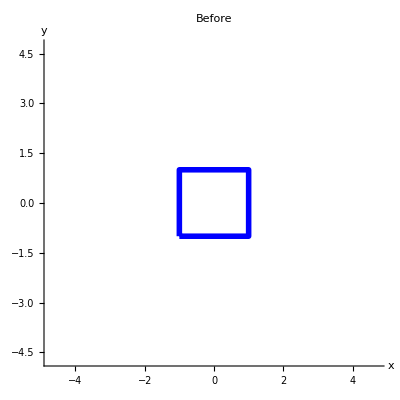

```mathematica
ranger=Max[{1.2,Norm[A.{1,0}]+Norm[A.{0,1}]}];
Show[Graphics[{Thickness[0.01],Blue,Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]}],PlotRange->{{-ranger,ranger},{-ranger,ranger}},Axes->True,AxesLabel->{"x","y"},PlotLabel->"Before"]
```

Here's what you get when you hit this square with A:

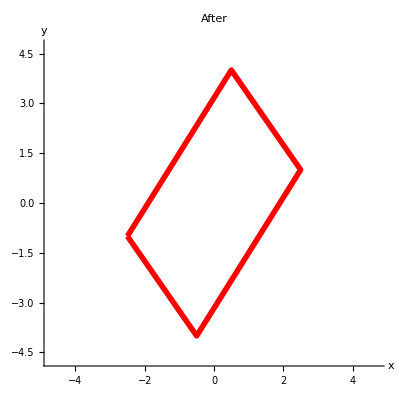

```mathematica
Show[Graphics[{Thickness[0.01],Red,Line[{A.{-1,-1},A.{1,-1},A.{1,1},A.{-1,1},A.{-1,-1}}]}],
     PlotRange->{{-ranger,ranger},{-ranger,ranger}},
     Axes->True,AxesLabel->{"x","y"},PlotLabel->"After"]
```

The determinant of A is:

```mathematica
Det[A]
```

-4.75

The area enclosed by the parallelogram is......................

#### L.25)

Here are two vectors X and Y and their plot:

{1.4,1.6}

{-2.5,2.5}

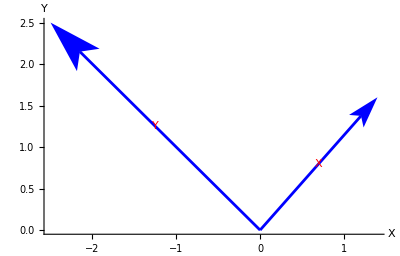

```mathematica
X = {0.2 Random[Integer,{4,10}],0.2Random[Integer,{4,10}]}
X;
Y = {-0.5 Random[Integer,{2,5}],0.5 Random[Integer,{2,5}]}
Y;
vectorplot = Show[Vector[X,Tail->{0,0},VectorColor->Blue],
		       Vector[Y,Tail->{0,0},VectorColor->Blue],
	Graphics[{Red,Text["X",X/2]}],	Graphics[{Red,Text["Y",Y/2]}],
	Axes->True,AxesLabel->{"X","Y"},PlotRange->All]
```

Here is the parallelogram these two vectors define:

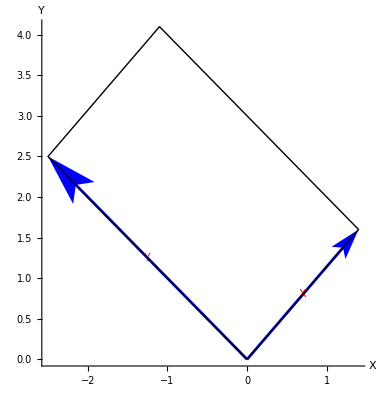

```mathematica
Show[vectorplot,
	   Graphics[Line[{{0,0},X,X+ Y,Y,{0,0}}]]]
```

Tell how you would use X and Y to set up a matrix A so that |Det[A]| calculates the  area of this parallelogram.
              A = (□ | □
□ | □)

#### L.26)

Here's a 2D matrix A:

```mathematica
A = {{0.7,1.8},{-0.8,0}};
MatrixForm[A]
```

(0.7 | 1.8
-0.8 | 0)

Here are A^t, the transpose of A, and A^-1, the inverse of A:

```mathematica
MatrixForm[Transpose[A]]
MatrixForm[Inverse[A]]
```

(0.7 | -0.8
1.8 | 0)

(0. | -1.25
0.555556 | 0.486111)

They don't look much alike. 
But see what they do when you hit both on the unit circle:

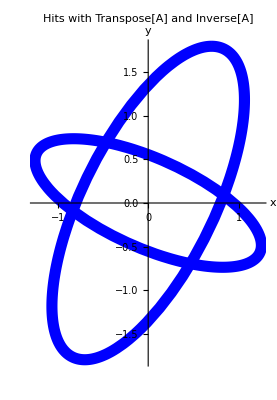

```mathematica
Clear[x,y,t,s];
{tlow,thigh}={0,2 π};
{x[t_],y[t_]}={Cos[t],Sin[t]};
Clear[hitplotter,hitpointplotter,pointcolor,actionarrows,matrix2D];
hitplotter[matrix2D_]:=ParametricPlot[matrix2D.{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.02],Blue}},AxesLabel->{"x","y"}];Show[hitplotter[Transpose[A]],hitplotter[Inverse[A]],PlotLabel->"Hits with Transpose[A] and Inverse[A]", PlotRange -> All]
```

Describe what you see and try to explain why you see it.
Some questions to ponder:
Both ellipses seem to be hanging on the same perpendicular frame. What perpendicular frame is it?
Why does the long axis of each ellipse line up with the short axis of the other?
When you multiply the area enclosed by one of the ellipses times the area enclosed by other ellipse, what do you get?

#### L.27)

Here's a random matrix A:

```mathematica
Clear[alignerframe];
s = Random[Real,{-Pi/2,Pi/2}];
{alignerframe[1],alignerframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
aligner = {alignerframe[1],alignerframe[2]};

{xstretch,ystretch} = {0.4 Random[Integer,{3,5}],0.3 Random[Integer,{1,3}]};
stretcher = {{xstretch,0},{0,ystretch}};

Clear[hangerframe];
s = Random[Real,{-Pi/2,Pi/2}];;
{hangerframe[1],hangerframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
hanger = Transpose[{hangerframe[1],hangerframe[2]}];
A = hanger.stretcher.aligner;
MatrixForm[A]
```

(0.582839 | 0.614546
-0.203922 | 1.02032)

Here is the square with corners at {-1,-1}, {1,-1},{1,1}, and {-1,1}:

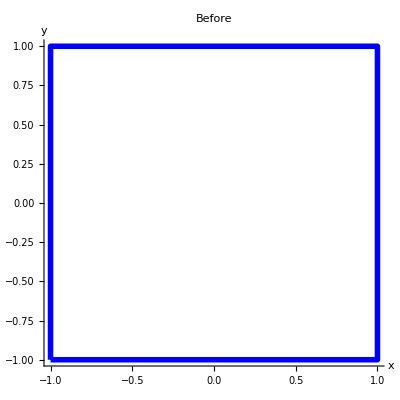

```mathematica
Show[Graphics[{Thickness[0.01],Blue,Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]}],PlotRange->All,Axes->True,AxesLabel->{"x","y"},PlotLabel->"Before"]
```

Here are the parallelograms you get what you get when you hit this square with this matrix and its transpose:

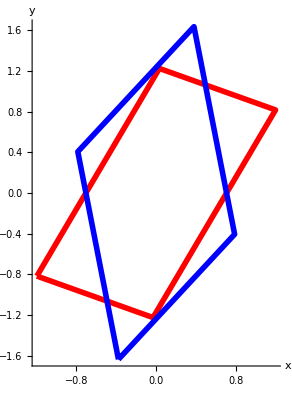

```mathematica
Ahit = Graphics[{Thickness[0.01],Red,Line[{A.{-1,-1},A.{1,-1},A.{1,1},A.{-1,1},A.{-1,-1}}]}];
B = Transpose[A];
transAhit =  Graphics[{Thickness[0.01],Blue,Line[{B.{-1,-1},B.{1,-1},B.{1,1},B.{-1,1},B.{-1,-1}}]}];

Show[Ahit,transAhit,PlotRange->All,  Axes->True,AxesLabel->{"x","y"}]
```

Express the measurement of area enclosed by one of these parallelograms in terms of the measurement of the area enclosed by the other.

#### L.28)

Here's a random matrix A:

```mathematica
Clear[alignerframe];
s = Random[Real,{-Pi/2,Pi/2}];
{alignerframe[1],alignerframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
aligner = {alignerframe[1],alignerframe[2]};

{xstretch,ystretch} = {0.4 Random[Integer,{3,5}],0.3 Random[Integer,{1,3}]};
stretcher = {{xstretch,0},{0,ystretch}};

Clear[hangerframe];
s = Random[Real,{-Pi/2,Pi/2}];
{hangerframe[1],hangerframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
hanger = Transpose[{hangerframe[1],hangerframe[2]}];
A = hanger.stretcher.aligner;
MatrixForm[A]
```

(1.83003 | 0.20588
-0.801304 | 0.237716)

Here is the square with corners at {0,0},{1,0},{1,1}, and{0,1}:

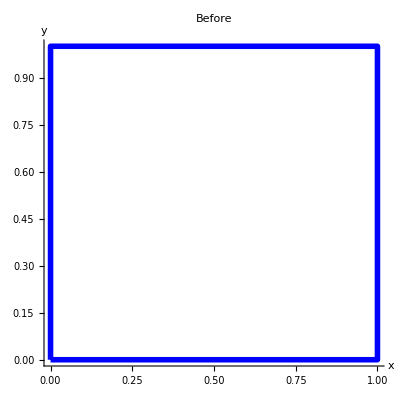

```mathematica
Show[Graphics[{Thickness[0.01],Blue,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}],PlotRange->All,Axes->True,AxesLabel->{"x","y"},PlotLabel->"Before"]
```

Here are the parallelograms you get what you get when you hit this square with this matrix and its inverse:

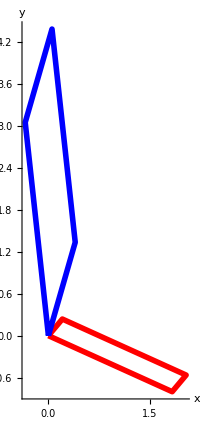

```mathematica
Ahit = Graphics[{Thickness[0.01],Red,Line[{A.{0,0},A.{1,0},A.{1,1},A.{0,1},A.{0,0}}]}];
B = Inverse[A];
invAhit = Graphics[{Thickness[0.01],Blue,Line[{B.{0,0},B.{1,0},B.{1,1},B.{0,1},B.{0,0}}]}];

Show[Ahit,invAhit,PlotRange->All, Axes->True,AxesLabel->{"x","y"}]
```

Express the measurement of area enclosed by one of these parallelograms in terms of the measurement of the area enclosed by the other.

## Hand Calculation Literacy

#### LHC.1) Determinants

Here's a random 2D matrix:

```mathematica
A={{Random[Integer,{-3,3}],Random[Integer,{-3,3}]},{Random[Integer,{-3,3}],Random[Integer,{-3,3}]}};

MatrixForm[A]
```

(-2 | 1
-1 | -1)

Give a hand calculation of the determinant of A.

#### LHC.2) Solving 2D systems by hand via the Cramer's rule formula

Here is a 2D linear system:

```mathematica
A={{Random[Integer,{1,3}],Random[Integer,{-3,3}]},{0.5 Random[Integer,{-3,3}],Random[Integer,{-8,-5}]}};
dim=2;
Clear[x,y];
Y={1,-1};

linearsystem = ColumnForm[Thread[A.{x[1],x[2]} ==  Y]]
```

2 x[1]+3 x[2]==1
-1.5 x[1]-6 x[2]==-1

Use the hand-style Cramer's rule to come up with the solution {x[1], x[2]}.

#### LHC.3) Inverting a 2D matrices by hand via the Cramer's rule formula

Here is a 2D matrix:

```mathematica
A={{Random[Integer,{1,3}],Random[Integer,{-3,3}]},{0.5 Random[Integer,{-3,3}],Random[Integer,{-8,-5}]}};
MatrixForm[A]
```

(1 | -3
-0.5 | -8)

Use hand-style Cramer's rule to come up with the inverse of A.